# Project member(s) (include name + student numbers) Harmen de Beurs (S4134524) Agne Danilaite (S4273702) Andzej Gedzo (S4074580) Nicolò Montalti (S4947231) Project 1 : Molecule Decelerator

## Introduction

For the research with certain kinds of molecules it is important that these molecules move very slowly. For this purpose a molecule decelerator is being developed. It consists of a sequence of many rings, which are put on high voltage (see the pictures below). For the understanding of the functioning of this device, it is very important to know the properties of the electric field that is being generated. In this project we will study that electric field and its properties.

-Graphics--Graphics-

## Coulomb Potential of Point Sources

Write a function to calculate the Coulomb potential at an arbitrary position (in 3D) due to a point source at another arbitrary position. Explain all the variables you introduce.

```mathematica
xyz = {x,y,z}(*[m] three dimention coordinate vairables for the arbitrary position where the potential is being evaluated*)
chargePosition = {x0,y0,z0} (*[m] three dimention coordinate variables for the position of the charge due to which there will be some potential*)
ϵ0 = QuantityMagnitude[Entity["PhysicalConstant", "ElectricConstant"]["Value"]] (*[F/m] value of the permitivity of the free space*)
charge = q (*[C] variable for the value of the charge due to which there will be potential*)

coulombPotential[charge_, chargePosition_, xyz_] := 1/(4*Pi*ϵ0) * charge / Sqrt[(xyz-chargePosition).(xyz-chargePosition)] (*function for potential (written based 
on griffiths introduction to electrodynamics formula 2.22) distance element is the square root of the dot product of the distance difference between charge and point where potential 
is measured*)
```

{x,y,z}

{x0,y0,z0}

8.85418781×10^-12

q

Calculate the electric field resulting from the Coulomb potential and confirm that the electric field is pointing away from a positive charge. Briefly explain your reasoning/approach.
-Graphics-

```mathematica
electricFieldSingleCharge = -Grad[coulombPotential[charge, chargePosition, xyz], xyz] (*electric field is equal to the negative gradient of the potential(formula 2.23)*)
Block[{q=1, x0=5, y0=2, z0=1}, VectorPlot3D[electricFieldSingleCharge, {x,4,6}, {y,1,3},{z,0,2}, PlotLabel->"Positive charge in (5,2,1)", AxesLabel->{"x","y","z"}]] (* electric field is simulated for a positive charge and can be seen pointing outward*)
Block[{q=-1, x0=-5, y0=2, z0=1}, VectorPlot3D[electricFieldSingleCharge, {x,-6,-4}, {y,1,3},{z,0,2}, PlotLabel->"Negative charge in (-5,2,1)", AxesLabel->{"x","y","z"}]] (* electric field is simulated for a negative charge and can be seen pointing inward*)
```

{(8.98755179×10^9 q (x-x0))/(((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2)),(8.98755179×10^9 q (y-y0))/(((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2)),(8.98755179×10^9 q (z-z0))/(((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2))}

-Graphics3D-

-Graphics3D-

Validate that your solution is the correct one, by showing that this electric field obeys Gauss’ law, as well as the Maxwell–Faraday equation (write down in words what conditions need to be met). Consider both the differential and integral forms, whichever is most appropriate. For example, do you “see” the correct charge enclosed in a closed surface?

```mathematica
(* To validate the solution, we analyze the electric field of a 1C charge in (0,0,0).*)
electricFieldCharge1 = Block[{q=1.0, x0=0, y0=0, z0=0}, electricFieldSingleCharge]

Curl[electricFieldCharge1, xyz]  (* Curl(E) = 0 for every x,y,z. If the solution is correct the result should be 0. (Maxwell-Faraday law)*)
Limit[Curl[electricFieldCharge1, xyz], xyz->{0,0,0}] (* Curl(E) = 0 even on the charge.*)

(*The following function computes the flux of a generic field through a sphere of radius sphereRadius centered in sphereCenter*)
fluxThroughSphere[field_, sphereCenter_, sphereRadius_] := Integrate[(field.(xyz-sphereCenter) / Sqrt[(xyz-sphereCenter).(xyz-sphereCenter)]), xyz ∈ Sphere[sphereCenter, sphereRadius]]

(* A position and a radius of the sphere are chosen to contain the charge inside.*)
sphereCenter = {0, 0, 0}
sphereRadius = 1
fluxThroughSphere[electricFieldCharge1, sphereCenter, sphereRadius] * ϵ0 
(* Because Flux(E) = q/ϵ0 (Gauss' law), the charge enclosed inside the sphere is 1C,
when the result is multiplied by ϵ0 the result should be equal to 1.*)

(* A position and a radius of the sphere are chosen not to contain the charge inside.*)
sphereCenter = {2.0, 3.0, -4.0}
sphereRadius = 1
fluxThroughSphere[electricFieldCharge1, sphereCenter, sphereRadius] * ϵ0
(* Flux(E) = 0, the charge enclosed inside the sphere is 0C. 
The flux through any surface enclosing the charge is q/ϵ0, because no charge is inside it is 0. The value obtained is very close to 0.*)
```

{(8.98755×10^9 x)/((x^2+y^2+z^2)^(3/2)),(8.98755×10^9 y)/((x^2+y^2+z^2)^(3/2)),(8.98755×10^9 z)/((x^2+y^2+z^2)^(3/2))}

{0.,0.,0.}

{0.,0.,0.}

{0,0,0}

1

1.

{2.,3.,-4.}

1

-8.75698×10^-19

Do the same for two (different) point sources some distance apart.

```mathematica
electricFieldCharge2 = Block[{q=-2.0, x0=1.0, y0=0, z0=0}, electricFieldSingleCharge] (*Value is assigned to the elctric field of the second charge.*)

(*Electric field values of the first and the second charge are summed to find the total electric field.*)
electricFieldDoubleCharge = electricFieldCharge1 + electricFieldCharge2 

Curl[electricFieldDoubleCharge, xyz] (* Curl(E) = 0 for every x,y,z*)

(*A position and radius of the sphere are chosen to contain both charges inside*)
sphereCenter = {0.5,0.0,0.0}
sphereRadius = 2
fluxThroughSphere[electricFieldDoubleCharge, sphereCenter, sphereRadius] * ϵ0 
(* Div(E) = q/ϵ0, q is inside the sphere. Because the sphere contains both charges (1C and -2C), total charge is -1C.*)

(*A position of the sphere is chosen to contain only the first charge inside*)
sphereCenter = {0.0,0.0,0.0}
sphereRadius = 0.5
fluxThroughSphere[electricFieldDoubleCharge, sphereCenter, sphereRadius] * ϵ0 
(* Div(E) = q/ϵ0, q is inside the sphere. Because the sphere contains only the first charge(1C), total charge is 1C. *)

(*A position of the sphere is chosen to contain only the second charge inside*)
sphereCenter = {1.0,0.0,0.0}
sphereRadius = 0.5
fluxThroughSphere[electricFieldDoubleCharge, sphereCenter, sphereRadius] * ϵ0 
(* Div(E) = q/ϵ0, q is inside the sphere. Because the sphere contains only the second charge(-2C), total charge is -2C.*)

(*A position of the sphere is chosen to contain no charge inside*)
sphereCenter = {4.0,0.0,0.0}
sphereRadius = 0.5
fluxThroughSphere[electricFieldDoubleCharge, sphereCenter, sphereRadius] * ϵ0 
(* Div(E) = q/ϵ0, q is inside the sphere. Because the sphere contains no charges, total charge is 0C.*)
```

{-(1.79751×10^10 (-1.+x))/(((-1.+x)^2+y^2+z^2)^(3/2)),-(1.79751×10^10 y)/(((-1.+x)^2+y^2+z^2)^(3/2)),-(1.79751×10^10 z)/(((-1.+x)^2+y^2+z^2)^(3/2))}

{-(1.79751×10^10 (-1.+x))/(((-1.+x)^2+y^2+z^2)^(3/2))+(8.98755×10^9 x)/((x^2+y^2+z^2)^(3/2)),-(1.79751×10^10 y)/(((-1.+x)^2+y^2+z^2)^(3/2))+(8.98755×10^9 y)/((x^2+y^2+z^2)^(3/2)),-(1.79751×10^10 z)/(((-1.+x)^2+y^2+z^2)^(3/2))+(8.98755×10^9 z)/((x^2+y^2+z^2)^(3/2))}

{0.,0.,0.}

{0.5,0.,0.}

2

-1.

{0.,0.,0.}

0.5

1.

{1.,0.,0.}

0.5

-2.

{4.,0.,0.}

0.5

-1.23898×10^-18

## Coulomb Potential of a Ring

Using the results obtained above, calculate the potential along the line through the center of a uniformly charged ring (how do you define the total charge on the ring?). 
-Graphics-
Figure 1. Derivation of the potential along the axis of a charged ring.

r

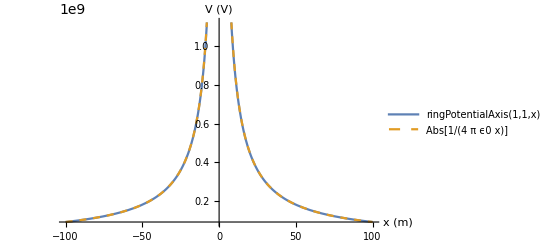

```mathematica
radius = r (*Radius of the ring*)
ringPotentialAxis[charge_, radius_, x_] := 1/(4*Pi*ϵ0) * charge / Sqrt[radius^2 + x^2] (*The equation for potential due to a ring of charge was derived analytically in Figure 1.*)
Plot[{ringPotentialAxis[1, 1, x], Abs[1/(4*Pi*ϵ0*x)]}, {x,-100,100}, AxesLabel->{"x (m)", "V (V)"}, PlotStyle->{Thick, Dashed}, PlotLegends->"Expressions"] (*Plot of the ring electric field along the axis.*)
```

What scaling behaviour do you recognize between the distance to the center and the radius of the ring?

ANSWER

Potential falls down as

Try to calculate the potential at an arbitrary position relative to the ring, so not on the axis through the center. Generously comment on your ideas, approach, implementation, and findings.
-Graphics-
Figure 2. Derivation of the potential on any point of a charged ring.

```mathematica
(*The equation of the potential on any point of a charged ring was derived in Figure 2.*)
generalRingPotential [charge_, radius_, xyz_]:= Integrate[coulombPotential[charge/(2*Pi*radius), {x0,y0,0}, xyz], {x0,y0} ∈ Circle[{0,0},radius]] 

(*To validate our solution, we evaluate the previous function on a point on the axes of the ring. Then we compare the result with the one given by ringPotentialAxis *)
xyzTest = {0, 0, xTest}
chargeTest = q
radiusTest = r

generalRingPotential[chargeTest, radiusTest, xyzTest] == ringPotentialAxis[chargeTest, radiusTest, xTest]
(* The two functions return the same value as long as r > 0, as expected*)
```

{0,0,xTest}

q

r

ConditionalExpression[True, r>0]

## Coulomb Potential of Many Rings

In the actual decelerator many rings are placed behind each other, as shown in the right picture at the beginning of the assignment. The rings are mounted on eight rods, so that every eighth ring carries the same voltage. The voltages on the rings, and their separation are chosen such that the potential on the axis through the rings approaches as closely as possible a harmonic pattern (=sine-wave with an arbitrary phase) with a period of  rings. Find out the largest deviation from a pure harmonic and show how the maximum electric field strength vary with the size and separation of the rings.

64

Sin[(i π)/4]

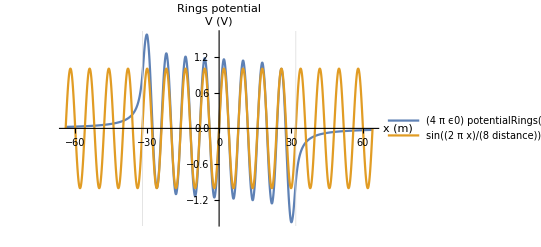

{1.41512,{x→-33.7713}}

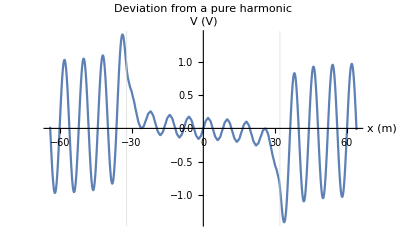

-(6.35515882×10^9 (-31 distance+x))/((r^2+(-31 distance+x)^2)^(3/2))-(8.98755179×10^9 (-30 distance+x))/((r^2+(-30 distance+x)^2)^(3/2))-(6.35515882×10^9 (-29 distance+x))/((r^2+(-29 distance+x)^2)^(3/2))+(6.35515882×10^9 (-27 distance+x))/((r^2+(-27 distance+x)^2)^(3/2))+(8.98755179×10^9 (-26 distance+x))/((r^2+(-26 distance+x)^2)^(3/2))+(6.35515882×10^9 (-25 distance+x))/((r^2+(-25 distance+x)^2)^(3/2))-(6.35515882×10^9 (-23 distance+x))/((r^2+(-23 distance+x)^2)^(3/2))-(8.98755179×10^9 (-22 distance+x))/((r^2+(-22 distance+x)^2)^(3/2))-(6.35515882×10^9 (-21 distance+x))/((r^2+(-21 distance+x)^2)^(3/2))+(6.35515882×10^9 (-19 distance+x))/((r^2+(-19 distance+x)^2)^(3/2))+(8.98755179×10^9 (-18 distance+x))/((r^2+(-18 distance+x)^2)^(3/2))+(6.35515882×10^9 (-17 distance+x))/((r^2+(-17 distance+x)^2)^(3/2))-(6.35515882×10^9 (-15 distance+x))/((r^2+(-15 distance+x)^2)^(3/2))-(8.98755179×10^9 (-14 distance+x))/((r^2+(-14 distance+x)^2)^(3/2))-(6.35515882×10^9 (-13 distance+x))/((r^2+(-13 distance+x)^2)^(3/2))+(6.35515882×10^9 (-11 distance+x))/((r^2+(-11 distance+x)^2)^(3/2))+(8.98755179×10^9 (-10 distance+x))/((r^2+(-10 distance+x)^2)^(3/2))+(6.35515882×10^9 (-9 distance+x))/((r^2+(-9 distance+x)^2)^(3/2))-(6.35515882×10^9 (-7 distance+x))/((r^2+(-7 distance+x)^2)^(3/2))-(8.98755179×10^9 (-6 distance+x))/((r^2+(-6 distance+x)^2)^(3/2))-(6.35515882×10^9 (-5 distance+x))/((r^2+(-5 distance+x)^2)^(3/2))+(6.35515882×10^9 (-3 distance+x))/((r^2+(-3 distance+x)^2)^(3/2))+(8.98755179×10^9 (-2 distance+x))/((r^2+(-2 distance+x)^2)^(3/2))+(6.35515882×10^9 (-distance+x))/((r^2+(-distance+x)^2)^(3/2))-(6.35515882×10^9 (distance+x))/((r^2+(distance+x)^2)^(3/2))-(8.98755179×10^9 (2 distance+x))/((r^2+(2 distance+x)^2)^(3/2))-(6.35515882×10^9 (3 distance+x))/((r^2+(3 distance+x)^2)^(3/2))+(6.35515882×10^9 (5 distance+x))/((r^2+(5 distance+x)^2)^(3/2))+(8.98755179×10^9 (6 distance+x))/((r^2+(6 distance+x)^2)^(3/2))+(6.35515882×10^9 (7 distance+x))/((r^2+(7 distance+x)^2)^(3/2))-(6.35515882×10^9 (9 distance+x))/((r^2+(9 distance+x)^2)^(3/2))-(8.98755179×10^9 (10 distance+x))/((r^2+(10 distance+x)^2)^(3/2))-(6.35515882×10^9 (11 distance+x))/((r^2+(11 distance+x)^2)^(3/2))+(6.35515882×10^9 (13 distance+x))/((r^2+(13 distance+x)^2)^(3/2))+(8.98755179×10^9 (14 distance+x))/((r^2+(14 distance+x)^2)^(3/2))+(6.35515882×10^9 (15 distance+x))/((r^2+(15 distance+x)^2)^(3/2))-(6.35515882×10^9 (17 distance+x))/((r^2+(17 distance+x)^2)^(3/2))-(8.98755179×10^9 (18 distance+x))/((r^2+(18 distance+x)^2)^(3/2))-(6.35515882×10^9 (19 distance+x))/((r^2+(19 distance+x)^2)^(3/2))+(6.35515882×10^9 (21 distance+x))/((r^2+(21 distance+x)^2)^(3/2))+(8.98755179×10^9 (22 distance+x))/((r^2+(22 distance+x)^2)^(3/2))+(6.35515882×10^9 (23 distance+x))/((r^2+(23 distance+x)^2)^(3/2))-(6.35515882×10^9 (25 distance+x))/((r^2+(25 distance+x)^2)^(3/2))-(8.98755179×10^9 (26 distance+x))/((r^2+(26 distance+x)^2)^(3/2))-(6.35515882×10^9 (27 distance+x))/((r^2+(27 distance+x)^2)^(3/2))+(6.35515882×10^9 (29 distance+x))/((r^2+(29 distance+x)^2)^(3/2))+(8.98755179×10^9 (30 distance+x))/((r^2+(30 distance+x)^2)^(3/2))+(6.35515882×10^9 (31 distance+x))/((r^2+(31 distance+x)^2)^(3/2))

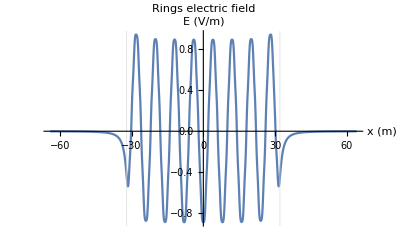

-Graphics3D-

```mathematica
numberRings = 64 (*Number of rings chosen to clearly depict the potential.*)

(*The total potential, as a function of the position, is calculated adding the potential generated by each ring.*)
chargeRingI = Sin[i*2*Pi/8] (*Charge on the ith ring*)
potentialRings[distance_, radius_, x_] := Sum[ringPotentialAxis[chargeRingI, radius, x-distance*i], {i, -numberRings/2, numberRings/2}]

(*Plot of the potential generated by 64 rings of radius 1 m separated by a distance of 1 m. Pure sine function of the same period for comparison.*)
Block[{distance=1, radius=1}, Plot[{(4*Pi*ϵ0) * potentialRings[distance, radius, x], Sin[2*Pi*x/(8*distance)]}, {x, -distance*numberRings, distance*numberRings}, AxesLabel->{"x (m)", "V (V)"}, GridLines->{{-distance*numberRings/2,distance*numberRings/2},{}}, GridLinesStyle->Thick, PlotLegends->"Expressions", PlotLabel->"Rings potential"]] 
(*
The potential is almost harmonic inside the region where the rings are placed. In the plot this region is indicated by two vertical lines.
Outside it falls down to 0, as expected.
*)

(*We are know ready to find the deviation of the potential from a pure harmonic. 
Setting the radius and the distance equal to 1, the maximum deviation is evaluated and a plot is made*)
deviationFromHarmonic[x_] := potentialRings[distance, radius, x] * (4*Pi*ϵ0)- Sin[x*2*Pi/(8*distance)]
maxDeviationFromHarmonic = Block[{distance=1, radius=1}, FindMaximum[deviationFromHarmonic[x], {x, -distance*numberRings/2}]]
Block[{distance=1, radius=1}, Plot[deviationFromHarmonic[x], {x, -distance*numberRings, distance*numberRings}, AxesLabel->{"x (m)", "V (V)"}, GridLines->{{-distance*numberRings/2,distance*numberRings/2},{}}, GridLinesStyle->Thick, PlotLabel->"Deviation from a pure harmonic"]]
(*
The maximum deviation from a pure harmonic is found at +/-33.7 m, just outside the regione where the rings are placed (-32 m < x < 32 m).
This can be easily seen by looking both at the plot and at the result of the FindMaximum function.
*)


(*We first find the electric field by evaluating the derivative of the potential. Because of the simmetry of the system, the only non-zero component of E is x.*)
electricFieldRings[x_] = -D[potentialRings[distance, radius, x], x]
Block[{r=1.0, distance=1.0}, Plot[electricFieldRings[x] * (4*Pi*ϵ0), {x,-distance*numberRings,distance*numberRings}, AxesLabel->{"x (m)", "E (V/m)"}, GridLines->{{-distance*numberRings/2,distance*numberRings/2},{}}, GridLinesStyle->Thick, PlotLabel->"Rings electric field"]]
(*Finally we calculate the maximum of E, as a funtion of the radius and the distance between the rings*)
maxElectricFieldRings[radius_, dist_] := Block[{r=radius, distance=dist}, FindMaximum[electricFieldRings[x], x][[1]]]
Plot3D[maxElectricFieldRings[r, d], {r, 0.5, 5}, {d, 0.5, 5}, AxesLabel->Automatic, PlotLabel->"Max(E) as a function of radius and distance"] (*This function will take a while to run*)
(*
In the last plot it can be easily noticed that E assumes bigger values for small values of the radius and the distance.
Moreover, as soon as the distance between the rings becomes greater than their radius, E immediately gets much smaller.
*)
```

## Feedback

We would appreciate to know how much time you spend on this project.

```mathematica
Time spend = 10h
```

If you have further comments on this problem that may be useful to improve subsequent problems, please let us know. Write your comments below.